## Buffon' s needle

A needle of unit length is thrown at random on a table where a few parallel lines are drawn at a unit distance :
 what is the probability that the needle will lie across one of these lines?

## PDF

```mathematica
Subscript[f, X,θ](x,θ) = 1/π χ[0,1](x)*χ[-π/2,π/2](θ)
```

```mathematica
Plot3D[PDF[UniformDistribution[{{0, 1},{ -π/2, π/2}} ], {x, y}], {x, 0, 1}, {y, -π/2, π/2}, PlotLabel -> Row[{"n = ", n}]]
Plot3D[CDF[UniformDistribution[{{0, 1},{ -π/2, π/2}} ], {x, y}], {x, 0, 1}, {y, -π/2, π/2}, PlotLabel -> Row[{"n = ", n}]]
```

-Graphics3D-

-Graphics3D-

### marginals

```mathematica
Subscript[f, X](x) = χ[0,1](x)
```

```mathematica
Subscript[f, θ](θ) = 1/π χ[-π/2,π/2](θ)
```

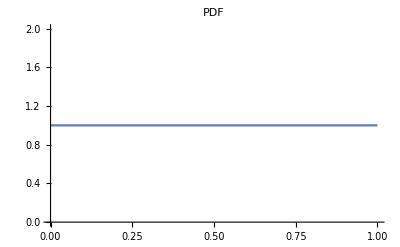

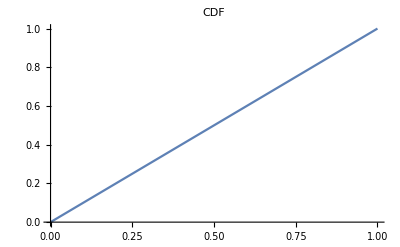

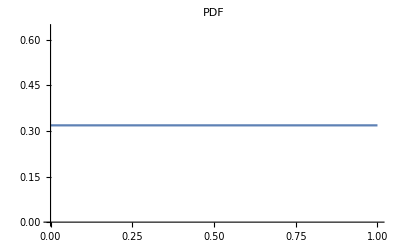

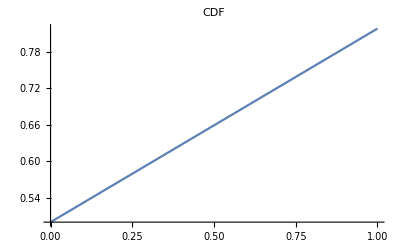

```mathematica
Plot[PDF[UniformDistribution[{0, 1} ], {x}], {x, 0, 1}, PlotLabel -> Row[{"PDF"}]]
Plot[CDF[UniformDistribution[{0, 1} ], {x}], {x, 0, 1}, PlotLabel -> Row[{"CDF"}]]
Plot[PDF[UniformDistribution[{ -π/2, π/2} ], {x}], {x, 0, 1}, PlotLabel -> Row[{"PDF"}]]
Plot[CDF[UniformDistribution[{ -π/2, π/2} ], {x}], {x, 0, 1}, PlotLabel -> Row[{"CDF"}]]
```

## Events

```mathematica
B={(x,θ): x≤1/2 cos(θ) ∨ x ≥1-1/2 cos(θ); -π/2≤θ≤π/2}
```

```mathematica
ParametricPlot3D[{x,θ,1},{x,Cos[θ]/2,1-Cos[θ]/2},{θ, -π/2,π/2},PlotStyle->{Red,Thickness[0.02]}]
```

ParametricPlot3D::plln: Limiting value Cos[θ]/2 in {x,Cos[θ]/2,1-Cos[θ]/2} is not a machine-sized real number.

ParametricPlot3D[{x,θ,1},{x,Cos[θ]/2,1-Cos[θ]/2},{θ,-π/2,π/2},PlotStyle→{Red,Thickness[0.02]}]

```mathematica
A={the needle lies across a line}={ω∈Ω:(X,Θ)∈B}
```

## Probability

```mathematica
P{A}=E[Subscript[I, A]]=E[Subscript[χ, B](X,Θ)]=E[E[Subscript[χ, B](X,Θ)|Θ]]=
=∫_(-π/2)^(π/2) E[Subscript[χ, B](X,θ)] dθ/π=1/π∫_(-π/2)^(-π/2) E[Subscript[χ, B](X,Θ)|Θ=θ]dθ





E[Subscript[χ, B](X,θ)]=P{X≤1/2 cos θ} ∪ {X≥1−1/2 cos(θ)}=1/2 cosθ+1/2 cosθ=cos θ





P{A}=1/π∫_(-π/2)^(-π/2) cos θdθ = 2/π
```